# Answers to Exercises Gaurav Kewalramani

# Week 1

```mathematica
RotI={1->5,2->11,3->13,4->6,5->12,6->7,7->4,8->17,9->22,10->26,11->14,12->20,13->15,14->23,15->25,16->8,17->24,18->21,19->19,20->16,21->1,22->9,23->2,24->18,25->3,26->10}
```

{1→5,2→11,3→13,4→6,5→12,6→7,7→4,8→17,9→22,10→26,11→14,12→20,13→15,14→23,15→25,16→8,17→24,18→21,19→19,20→16,21→1,22→9,23→2,24→18,25→3,26→10}

```mathematica
Graph[RotI]
```

-Graphics-

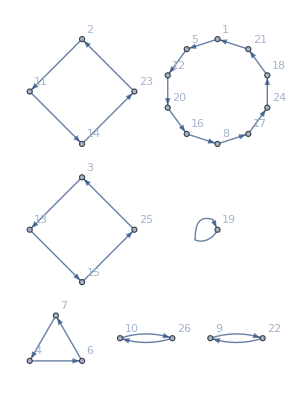

```mathematica
Graph[RotI,VertexLabels->"Name"]
```

```mathematica
RotIinv={5->1,11->2,13->3,6 -> 4, 12->5, 7->6, 4->7,17->8,22->9,26->10,14->11,20->12,15->13,23->14,25->15,8->16,24->17,21->18,19->19,16->20,1->21,9->22,2->23,18->24,3->25,10->26}
```

{5→1,11→2,13→3,6→4,12→5,7→6,4→7,17→8,22→9,26→10,14→11,20→12,15→13,23→14,25→15,8→16,24→17,21→18,19→19,16→20,1→21,9→22,2→23,18→24,3→25,10→26}

```mathematica
Graph[RotIinv]
```

-Graphics-

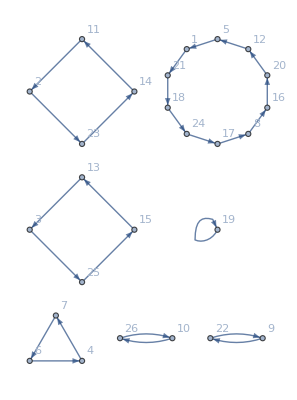

```mathematica
Graph[RotIinv,VertexLabels->"Name"]
```

```mathematica
lettercodes = {"a" -> 1,"b"->2,"c"->3,"d"->4,"e"->5,"f" ->6,"g"->7,"h"->8,"i"->9,"j"->10,"k"->11,"l"->12,"m"->13,"n"->14,"o"->15,"p"->16,"q"->17,"r"->18,"s"->19,"t"->20,"u"->21,"v"->22,"w"->23,"x"->24,"y"->25,"z"->26}
```

{a→1,b→2,c→3,d→4,e→5,f→6,g→7,h→8,i→9,j→10,k→11,l→12,m→13,n→14,o→15,p→16,q→17,r→18,s→19,t→20,u→21,v→22,w→23,x→24,y→25,z→26}

```mathematica
ReplaceAll[ReplaceAll[lettercodes,RotI],RotIinv]
```

{a→1,b→2,c→3,d→4,e→5,f→6,g→7,h→8,i→9,j→10,k→11,l→12,m→13,n→14,o→15,p→16,q→17,r→18,s→19,t→20,u→21,v→22,w→23,x→24,y→25,z→26}

```mathematica
RefB={1->25,25->1,2->18,18->2,3->21,21->3,4->8,8->4,5->17,17->5,6->19,19->6,7->12,12->7,9->16,16->9,10->24,24->10,11->14,14->11,13->15,15->13,20->26,26->20,22->23,23->22}
```

{1→25,25→1,2→18,18→2,3→21,21→3,4→8,8→4,5→17,17→5,6→19,19→6,7→12,12→7,9→16,16→9,10→24,24→10,11→14,14→11,13→15,15→13,20→26,26→20,22→23,23→22}

```mathematica
ReplaceAll[ReplaceAll[lettercodes,RefB],RefB]
```

{a→1,b→2,c→3,d→4,e→5,f→6,g→7,h→8,i→9,j→10,k→11,l→12,m→13,n→14,o→15,p→16,q→17,r→18,s→19,t→20,u→21,v→22,w→23,x→24,y→25,z→26}

### //** Questions Starts From Here **//

```mathematica
Table[Replace[Replace[Replace[x,RotI],RefB],RotIinv],{x,1,26,1}]
```

{8,11,13,19,6,5,16,1,14,12,2,10,3,9,21,7,26,25,4,22,15,20,24,23,18,17}

```mathematica
{1->8,8->1,2->11,3->13,4->19,5->6,6->5,7->16,8->1,9->14,10->12,11->2,12->10,13->3,14->9,15->21,16->7,17->26,18->25,19->4,20->22,21->15,22->20,23->24,24->23,25->18,26->17}
```

{1→8,8→1,2→11,3→13,4→19,5→6,6→5,7→16,8→1,9→14,10→12,11→2,12→10,13→3,14→9,15→21,16→7,17→26,18→25,19→4,20→22,21→15,22→20,23→24,24→23,25→18,26→17}

```mathematica
EnigmaGuts={1->8,8->1,2->11,3->13,4->19,5->6,6->5,7->16,8->1,9->14,10->12,11->2,12->10,13->3,14->9,15->21,16->7,17->26,18->25,19->4,20->22,21->15,22->20,23->24,24->23,25->18,26->17}
```

{1→8,8→1,2→11,3→13,4→19,5→6,6→5,7→16,8→1,9→14,10→12,11→2,12→10,13→3,14→9,15→21,16→7,17→26,18→25,19→4,20→22,21→15,22→20,23→24,24→23,25→18,26→17}

```mathematica
Table[ReplaceAll[x,EnigmaGuts],{x,1,26,1}]
```

{8,11,13,19,6,5,16,1,14,12,2,10,3,9,21,7,26,25,4,22,15,20,24,23,18,17}

```mathematica
Table[ReplaceAll[x,EnigmaGuts],{x,1,26,1}]
```

{8,11,13,19,6,5,16,1,14,12,2,10,3,9,21,7,26,25,4,22,15,20,24,23,18,17}

```mathematica
Enigma1[x_,n_]:=Mod[((Replace[Mod[x+n,26,1],EnigmaGuts])-n),26,1]
```

```mathematica
Table[Enigma1[1,n],{n,0,25,1}]
```

{8,10,11,16,2,26,10,20,6,3,18,25,17,22,7,18,10,8,12,3,21,25,2,26,20,18}

```mathematica
list1 = Range[0, 25];
```

```mathematica
list2= {8,10,11,16,2,26,10,20,6,3,18,25,17,22,7,18,10,8,12,3,21,25,2,26,20,18};
```

```mathematica
MapThread[Enigma1,{list2,list1}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

# Week 2

```mathematica
EnigmaMachine[text_,key_]:=MapThread[Enigma1,{text,Table[key+i,{i,0,Length[text]-1}]}]
```

```mathematica
EnigmaMachine[{1,2,3,4,5},28]
```

{11,3,12,9,22}

```mathematica
EnigmaMachine[EnigmaMachine[{1,2,3,4,5},28],28]
```

{1,2,3,4,5}

```mathematica
plain={1,3,4,23,9,2,12,8}
```

{1,3,4,23,9,2,12,8}

```mathematica
cypher={17,4,14,6,17,3,4,23,8,8,19,3,1,24,22,11,6,22,15}
```

{17,4,14,6,17,3,4,23,8,8,19,3,1,24,22,11,6,22,15}

//** cypher text here in letter is ....   QDNFQCDWHHSCAXVKFVO
         Plain Text here in letters is ....    ACDWIBLH
         the valid positions here can be 1,4,6,7,8,9,10 and 12. (checked online on the Enigma Crib Analysis by putting the cipher text and plain text, and why it can’t be 2,3 and 5 is because it has clashes, meaning they are invalid crib.)
          Now, if we take the position 1 and check then there is actually no cycle being made I can explain this, so in position 1 the cyfrag will be {17,4,14,6,17,3,4,23} now if we try to make a cycle here there will be none as [A ->Q ], [C->D then D ->N and then that’s it no more movement],[ W->F], [I->Q], [B->C then  C->D then D->N but then that’s it], its not a full cycle similarly for the rest.
          
          Now we know that at position 1 there’s no crib cycle even though its a valid crib, A valid crib doesn’t mean there will be a crib cycle, so now checking for position 4. 
          so for position 4, the plain text will remain the same but the cyfrag will be {6,17,3,4,23,8,8,19} now if we try to make a crib cycle here again like position 1 there’s no crib cycle here too I can again explain this as, [A ->F],[C->Q],[D->C then C->Q it’s not a cycle], [W->D then D->C then C->Q it’s not a cycle] , [I->W then W ->D then its the same as second step I did in this so again no full cycle after Q],[B->H the H->S then that’s it], so basically for there’s no full cycle for any of it. hence position 4 has no crib cycle too. Now we move to the next position that is position 6
          
          Now for position 6 the cyfrag will be {3,4,23,8,8,19,3,1} we will find that there’s actually a crib cycle here, how? I can explain so.... [  A -> C then C ->D then D -> W then W -> H then H -> A then its A again hence its’s a full cycle as now A will again go to C and the cycle will repeat itself ], HENCE 6th POSITION IS WHERE WE FOUND OUR FIRST CRIB CYCLE 
          
          So the distance between each member in the crib cycle will be 1,2,3,4,8 i.e A,C,D,W,H (how we getting this? if we see the plain text we see the position of A is 1, C is 2, D is 3, W is 4 and H is 8. the plain text again for reference is ACDWIBLH)     **//
          
          
          So, Now we know that 6th position is where we found our first crib cycle, there can be more positions after 6 where a crib cycle exists but we were advised in the assignment that if there’re more than one crib cycle then use the first one so I found the first one at 6. Now, moving on with the 6th position to complete the assignment, we have cyfrag as {3,4,23,8,8,19,3,1} then we have to write Bombe function according to the crib cycle that I explained in the above paragraph for position 6.

```mathematica
cyfrag={3,4,23,8,8,19,3,1}
```

{3,4,23,8,8,19,3,1}

```mathematica
Bombe[plain_,cyfrag_,k_]:=
If[Enigma1[plain[[1]],k]==cyfrag[[1]]&&cyfrag[[1]]==plain[[1+1]]&&
Enigma1[plain[[2]],k+1]==cyfrag[[2]]&&cyfrag[[2]]==plain[[3]]&&
Enigma1[plain[[3]],k+2]==cyfrag[[3]]&&cyfrag[[3]]==plain[[4]]&&
Enigma1[plain[[4]],k+3]==cyfrag[[4]]&&cyfrag[[4]]==plain[[8]]&&
Enigma1[plain[[8]],k+7]==cyfrag[[8]]&&cyfrag[[8]]==plain[[1]],
{"YES!!!",k},
{"no"}
]
```

```mathematica
Table[Bombe[plain,cyfrag,k],{k,0,25,1}]
```

{{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{YES!!!,19},{no},{no},{no},{no},{no},{no}}

```mathematica
{{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"YES!!!",19},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"}}
```

{{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{no},{YES!!!,19},{no},{no},{no},{no},{no},{no}}

//** here the Bombe Function gave us a yes at 19 basically meaning it gave us a key 19 , this is the key setting that the bombe function gave us. Now the key calculation for the start of the whole cypher text should be : - 

( ( Key that Bombe Function gave us - ( crib start position -1 ) ) Mod 26, Now solving this :-

(19 - (6-1)) mod 26 = 14 , solving this will give us 14. Hence k = 14.

So, key for the start of the whole cypher text is 14.  **//

```mathematica
EnigmaMachine[{17,4,14,6,17,3,4,23,8,8,19,3,1,24,22,11,6,22,15},14]
```

{18,15,3,7,22,1,3,4,23,9,2,12,8,17,21,6,8,3,9}

//** Here we can see that if we use the enigma machine with the key k =14 will give us {18,15,3,7,22,1,3,4,23,9,2,12,8,17,21,6,8,3,9} which is if we write them as letters will be {ROCGVACDWIBLHQUFHCI} which basically has our plain text in it, our plain text is  {1,3,4,23,9,2,12,8} or in letter code {ACDWIBLH} and this is basically decryption of our cypher text by using the key we got from after using bombe function then getting the key for the start of the cypher text. **//

```mathematica
EnigmaMachine[{18,15,3,7,22,1,3,4,23,9,2,12,8,17,21,6,8,3,9},14]
```

{17,4,14,6,17,3,4,23,8,8,19,3,1,24,22,11,6,22,15}